# Reconstruct zeta2, psi1, psi2 from zeta1

Given any solution y(x)=zeta1(x) of the fourth-order zeta1 ODE, this notebook derives zeta2, psi1, and psi2 directly from y and its derivatives. The important part is the algebraic elimination in Sections 3 and 4.

## 1. Setup

```mathematica
ClearAll["Global`*"];
$Assumptions = Element[{x, lam}, Reals] && x > 0 && lam > 0;

odeZeta1[y_] := x^2 D[y, {x, 4}] + 4 x (1 + I x) D[y, {x, 3}] +
   2 x (5 I - 2 x) D[y, {x, 2}] - 2 (I + 2 x) D[y, x] - lam^2 y;

(* Coefficients of the first-order system:
   zeta1' = A psi1 + B psi2
   zeta2' = C psi1 + D psi2
   psi1'  = E zeta1 + F zeta2
   psi2'  = G zeta1 + H zeta2 *)
coefA = I lam/(2 x^2) (I x - 1);
coefB = I lam/(2 x^2) (I x + 1) Exp[-2 I x];
coefC = I lam/(2 x^2) (I x - 1) Exp[2 I x];
coefD = I lam/(2 x^2) (I x + 1);
coefE = I lam/(2 x^2) (-(I x + 1));
coefF = I lam/(2 x^2) (I x + 1) Exp[-2 I x];
coefG = I lam/(2 x^2) (I x - 1) Exp[2 I x];
coefH = I lam/(2 x^2) (-(I x - 1));
```

## 2. Final reconstruction map

These are the formulas we want to derive. The next sections show how they are obtained from the first-order system.

```mathematica
psi1From[y_] := ((I x^2 + x) D[y, {x, 2}] + (-2 x^2 + 3 I x + 2) D[y, x])/(lam x);

psi2From[y_] := -I Exp[2 I x] ((x^2 + I x) D[y, {x, 2}] + (x + 2 I) D[y, x])/(lam x);

zeta2From[y_] := Exp[2 I x] (lam^2 y - 2 I x^2 D[y, {x, 3}] +
      4 x (x - I) D[y, {x, 2}] + 4 (x + I) D[y, x])/lam^2;
```

## 3. Algebraic derivation, step 1: differentiate zeta1 once

Set y0=y, y1=y', y2=y'', y3=y'''. We treat psi1, psi2, zeta2 as algebraic unknowns p1, p2, z2. The total derivative Dx uses the first-order system whenever p1, p2, or z2 are differentiated.

```mathematica
ClearAll[y0, y1, y2, y3, y4, p1, p2, z2];

p1Prime = coefE y0 + coefF z2;
p2Prime = coefG y0 + coefH z2;
z2Prime = coefC p1 + coefD p2;

Dx[expr_] := D[expr, x] + D[expr, y0] y1 + D[expr, y1] y2 +
   D[expr, y2] y3 + D[expr, y3] y4 +
   D[expr, p1] p1Prime + D[expr, p2] p2Prime + D[expr, z2] z2Prime;

rhs1 = coefA p1 + coefB p2;
eqFirst = y1 == rhs1;

rhs2 = FullSimplify[Dx[rhs1], Assumptions -> $Assumptions];
eqSecond = y2 == rhs2;

{eqFirst, eqSecond} // TraditionalForm
```

{y1==(ⅈ lam p1 (-1+ⅈ x))/(2 x^2)+(ⅈ lam p2 ⅇ^(-2 ⅈ x) (1+ⅈ x))/(2 x^2),y2==(lam ⅇ^(-2 ⅈ x) (p1 ⅇ^(2 ⅈ x) (x+2 ⅈ)+p2 ((3+2 ⅈ x) x-2 ⅈ)))/(2 x^3)}

A useful cancellation happens: after differentiating zeta1', the expression for y'' contains only psi1 and psi2, not zeta2. That is why the first two equations can solve for psi1 and psi2.

```mathematica
zeta2CoefficientInSecondDerivative = FullSimplify[Coefficient[Together[rhs2], z2], Assumptions -> $Assumptions]

psiSolutions = Solve[{eqFirst, eqSecond}, {p1, p2}] // FullSimplify;
psiSolutions // TraditionalForm

p1Formula = p1 /. First[psiSolutions];
p2Formula = p2 /. First[psiSolutions];

{p1Formula, p2Formula} // TraditionalForm
```

0

{{p1→((2+(-2 x+3 ⅈ) x) y1+(1+ⅈ x) x y2)/(lam x),p2→(ⅇ^(2 ⅈ x) ((2-ⅈ x) y1+(1-ⅈ x) x y2))/(lam x)}}

{((2+(-2 x+3 ⅈ) x) y1+(1+ⅈ x) x y2)/(lam x),(ⅇ^(2 ⅈ x) ((2-ⅈ x) y1+(1-ⅈ x) x y2))/(lam x)}

Thus psi1 and psi2 are already determined by y' and y''.

## 4. Algebraic derivation, step 2: differentiate one more time

Now differentiate y'' once more. This produces y''' and introduces zeta2 through psi1' and psi2'. Substituting the psi1 and psi2 formulas leaves one algebraic equation for zeta2.

```mathematica
rhs3BeforeSubstitution = FullSimplify[Dx[rhs2], Assumptions -> $Assumptions];

rhs3 = FullSimplify[rhs3BeforeSubstitution /. First[psiSolutions], Assumptions -> $Assumptions];
eqThird = y3 == rhs3;

zeta2Solution = Solve[eqThird, z2] // FullSimplify;
zeta2Solution // TraditionalForm

z2Formula = z2 /. First[zeta2Solution];
z2Formula // TraditionalForm
```

{{z2→(ⅇ^(2 ⅈ x) (lam^2 y0-2 ⅈ x^2 y3+4 (x+ⅈ) y1+4 x (x-ⅈ) y2))/lam^2}}

(ⅇ^(2 ⅈ x) (lam^2 y0-2 ⅈ x^2 y3+4 (x+ⅈ) y1+4 x (x-ⅈ) y2))/lam^2

This completes the elimination: {y',y''} gives psi1 and psi2, and y''' gives zeta2.

## 5. Convert the algebraic formulas into functions of y(x)

```mathematica
toFunctionRules = {
   y0 -> y[x],
   y1 -> D[y[x], x],
   y2 -> D[y[x], {x, 2}],
   y3 -> D[y[x], {x, 3}]
};

psi1Derived = FullSimplify[p1Formula /. toFunctionRules, Assumptions -> $Assumptions];
psi2Derived = FullSimplify[p2Formula /. toFunctionRules, Assumptions -> $Assumptions];
zeta2Derived = FullSimplify[z2Formula /. toFunctionRules, Assumptions -> $Assumptions];

{psi1Derived, psi2Derived, zeta2Derived} // TraditionalForm

checkAgainstDefinitions = FullSimplify[
   {psi1Derived - psi1From[y[x]], psi2Derived - psi2From[y[x]], zeta2Derived - zeta2From[y[x]]},
   Assumptions -> $Assumptions]
```

{((1+ⅈ x) x y''(x)+(2+(-2 x+3 ⅈ) x) y'(x))/(lam x),(ⅇ^(2 ⅈ x) ((1-ⅈ x) x y''(x)+(2-ⅈ x) y'(x)))/(lam x),(ⅇ^(2 ⅈ x) (lam^2 y(x)-2 ⅈ x^2 y^(3)(x)+4 x (x-ⅈ) y''(x)+4 (x+ⅈ) y'(x)))/lam^2}

{0,0,0}

Expected: checkAgainstDefinitions = {0,0,0}.

## 6. Direct verification of the original first-order system

The reconstructed functions satisfy three equations identically. The remaining zeta2 equation is proportional to the fourth-order zeta1 equation, so it vanishes whenever y solves the zeta1 ODE.

```mathematica
ClearAll[y];

z1 = y[x];
z2rec = zeta2From[z1];
p1rec = psi1From[z1];
p2rec = psi2From[z1];

resZeta1 = FullSimplify[D[z1, x] - (coefA p1rec + coefB p2rec), Assumptions -> $Assumptions]

resPsi1 = FullSimplify[D[p1rec, x] - (coefE z1 + coefF z2rec), Assumptions -> $Assumptions]

resPsi2 = FullSimplify[D[p2rec, x] - (coefG z1 + coefH z2rec), Assumptions -> $Assumptions]

resZeta2 = FullSimplify[D[z2rec, x] - (coefC p1rec + coefD p2rec), Assumptions -> $Assumptions]

zeta2ResidualCheck = FullSimplify[resZeta2 + 2 I Exp[2 I x] odeZeta1[z1]/lam^2, Assumptions -> $Assumptions]
```

0

0

0

(2 ⅇ^(2 ⅈ x) (ⅈ lam^2 y[x]+(-2+4 ⅈ x) y'[x]+x (2 (5+2 ⅈ x) y''[x]+4 (-ⅈ+x) y^(3)[x]-ⅈ x y^(4)[x])))/lam^2

0

Expected: resZeta1=0, resPsi1=0, resPsi2=0, and zeta2ResidualCheck=0. Equivalently, resZeta2=-(2 I Exp[2 I x]/lam^2) odeZeta1[y[x]].

## 7. Use with the zeta1 basis

After defining your four zeta1 basis functions, apply the reconstruction map to each one.

```mathematica
zeta1basis = {
(1-I*lam)LaguerreL[I*lam/2,-2*I*x]+I*lam*Hypergeometric1F1[1-I*lam/2,2,-2*I*x], 
(1+I*lam)LaguerreL[-I*lam/2,-2*I*x]-I*lam*Hypergeometric1F1[1+I*lam/2,2,-2*I*x],(1-I*lam)HypergeometricU[-I*lam/2,1,-2*I*x]-I*lam*HypergeometricU[1-I*lam/2,2,-2*I*x],
(1+I*lam)HypergeometricU[I*lam/2,1,-2*I*x]+I*lam*HypergeometricU[1+I*lam/2,2,-2*I*x]};
```

```mathematica
fullSystemBasis = FullSimplify[Table[
   {zeta1basis[[j]],
    zeta2From[zeta1basis[[j]]],
    psi1From[zeta1basis[[j]]],
    psi2From[zeta1basis[[j]]]},
   {j, Length[zeta1basis]}
],Assumptions->{x∈PositiveReals,lam∈PositiveReals}];
```

```mathematica
Bmat=fullSystemBasis;

cvec={c1,c2,c3,c4};

(*cvec.Bmat;*)
```

# Matching solutions for a rectangular function coupling

The four ’s solutions are

```mathematica
Bmat[[1]][[1]]
Bmat[[2]][[1]]
Bmat[[3]][[1]]
Bmat[[4]][[1]]
```

ⅈ lam Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+(1-ⅈ lam) LaguerreL[(ⅈ lam)/2,-2 ⅈ x]

-ⅈ lam Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]+(1+ⅈ lam) LaguerreL[-(ⅈ lam)/2,-2 ⅈ x]

-ⅈ lam HypergeometricU[1-(ⅈ lam)/2,2,-2 ⅈ x]+(1-ⅈ lam) HypergeometricU[-(ⅈ lam)/2,1,-2 ⅈ x]

ⅈ lam HypergeometricU[1+(ⅈ lam)/2,2,-2 ⅈ x]+(1+ⅈ lam) HypergeometricU[(ⅈ lam)/2,1,-2 ⅈ x]

The four ’s solutions are

```mathematica
Bmat[[1]][[2]]
Bmat[[2]][[2]]
Bmat[[3]][[2]]
Bmat[[4]][[2]]
```

1/lam^2 ⅇ^(2 ⅈ x) (-(4 (ⅈ+lam) (-4 ⅈ+lam) (-2 ⅈ+lam+(4+lam (-ⅈ+lam)) x+2 lam x^2) Hypergeometric1F1[-1-(ⅈ lam)/2,2,-2 ⅈ x])/(-2 ⅈ+lam)+ⅈ lam (4+lam (-2 ⅈ+lam+4 x)) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+lam^2 (-2 ⅈ+lam) x Hypergeometric1F1[1-(ⅈ lam)/2,3,-2 ⅈ x]+((1-ⅈ lam) (32 (-ⅈ+x)+lam (16+lam^2+16 x (-ⅈ+x)+2 lam (-ⅈ+6 x))) LaguerreL[1+(ⅈ lam)/2,-2 ⅈ x])/(-2 ⅈ+lam))

1/lam^2 ⅇ^(2 ⅈ x) ((4 (4+lam (3 ⅈ+lam)) (-2 ⅈ+4 x+lam (-1+(ⅈ+lam-2 x) x)) Hypergeometric1F1[-1+(ⅈ lam)/2,2,-2 ⅈ x])/(2 ⅈ+lam)-ⅈ lam (4+lam (2 ⅈ+lam-4 x)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]-lam^2 (2 ⅈ+lam) x Hypergeometric1F1[1+(ⅈ lam)/2,3,-2 ⅈ x]+((1+ⅈ lam) (-32 (-ⅈ+x)+lam (16+lam^2+lam (2 ⅈ-12 x)+16 x (-ⅈ+x))) LaguerreL[1-(ⅈ lam)/2,-2 ⅈ x])/(2 ⅈ+lam))

-1/(16 x^3)ⅈ ⅇ^(2 ⅈ x) ((6 ⅈ+lam) (2 ⅈ+lam (ⅈ+lam) x) HypergeometricU[-(ⅈ lam)/2,-3,-2 ⅈ x]+2 (6+lam x (2-3 ⅈ lam+2 (ⅈ+lam) x)) HypergeometricU[-(ⅈ lam)/2,-2,-2 ⅈ x])

1/(16 x^3)ⅈ ⅇ^(2 ⅈ x) ((-6 ⅈ+lam) (2 ⅈ+lam (-ⅈ+lam) x) HypergeometricU[(ⅈ lam)/2,-3,-2 ⅈ x]+2 (-6+lam (2+lam (3 ⅈ-2 x)+2 ⅈ x) x) HypergeometricU[(ⅈ lam)/2,-2,-2 ⅈ x])

The four ’s solutions are

```mathematica
Bmat[[1]][[3]]
Bmat[[2]][[3]]
Bmat[[3]][[3]]
Bmat[[4]][[3]]
```

(-ⅈ+lam (-2+ⅈ/x-2 ⅈ x)+2 x) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+1/2 (2 ⅈ+lam) (ⅈ x+lam (-ⅈ+x)) Hypergeometric1F1[2-(ⅈ lam)/2,3,-2 ⅈ x]

1/(2 x)((2 (ⅈ-2 x) x+lam (2 ⅈ-4 x-4 ⅈ x^2)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]-(-2 ⅈ+lam) x (-ⅈ x+lam (-ⅈ+x)) Hypergeometric1F1[2+(ⅈ lam)/2,3,-2 ⅈ x])

2 (lam-x+ⅈ lam x) HypergeometricU[1-(ⅈ lam)/2,3,-2 ⅈ x]+((lam-x) HypergeometricU[-(ⅈ lam)/2,0,-2 ⅈ x])/(2 x^2)

2 (lam+x+ⅈ lam x) HypergeometricU[1+(ⅈ lam)/2,3,-2 ⅈ x]+((lam+x) HypergeometricU[(ⅈ lam)/2,0,-2 ⅈ x])/(2 x^2)

The four ’s solutions are

```mathematica
Bmat[[1]][[4]]
Bmat[[2]][[4]]
Bmat[[3]][[4]]
Bmat[[4]][[4]]
```

-1/(2 x)ⅇ^(2 ⅈ x) (2 ⅈ (-lam+x+2 ⅈ lam x+2 (-ⅈ+lam) x^2) Hypergeometric1F1[1-(ⅈ lam)/2,2,-2 ⅈ x]+(-2 ⅈ+lam) x (-ⅈ x+lam (ⅈ+x)) Hypergeometric1F1[1-(ⅈ lam)/2,3,-2 ⅈ x])

1/(2 x)ⅇ^(2 ⅈ x) ((2 x (ⅈ+2 x)+lam (2 ⅈ+4 x-4 ⅈ x^2)) Hypergeometric1F1[1+(ⅈ lam)/2,2,-2 ⅈ x]+(2 ⅈ+lam) x (ⅈ x+lam (ⅈ+x)) Hypergeometric1F1[1+(ⅈ lam)/2,3,-2 ⅈ x])

1/(8 x^3)ⅇ^(2 ⅈ x) ((4 ⅈ+lam) (lam-x) HypergeometricU[-(ⅈ lam)/2,-2,-2 ⅈ x]+2 (2 ⅈ x+lam^2 x (ⅈ+x)+ⅈ lam (-2+x^2)) HypergeometricU[-(ⅈ lam)/2,-1,-2 ⅈ x])

-1/(8 x^3)ⅇ^(2 ⅈ x) ((-4 ⅈ+lam) (lam+x) HypergeometricU[(ⅈ lam)/2,-2,-2 ⅈ x]+2 (2 ⅈ lam+ⅈ (2+lam^2) x+lam (-ⅈ+lam) x^2) HypergeometricU[(ⅈ lam)/2,-1,-2 ⅈ x])

Let’s compute the constant vector  by matching the in- and feature-regions’ solutions at , as

```mathematica
Vin1={1,0,0,0};
Vin2={0,0,1,0};

cvec1={c11,c12,c13,c14};
cvec2={c21,c22,c23,c24};

eqs1=Thread[(cvec1.(Bmat/. x->(k/H)*Exp[-N1]))==Vin1];
eqs2=Thread[(cvec2.(Bmat/. x->(k/H)*Exp[-N1]))==Vin2];

solC1=Solve[eqs1,cvec1][[1]];
solC2=Solve[eqs2,cvec2][[1]];
```

where the solutions are horrible, but exist.

Let’s save these results in advanced,

```mathematica
DumpSave["matchingResults.mx",{solC1,solC2,Bmat}];
```

and we can recover them directly using

```mathematica
Get["matchingResults.mx"]
```

Finally, the out-region solutions, for every , would be given by

```mathematica
Vin1={1,0,0,0};
Vin2={0,0,1,0};

cvec1={c11,c12,c13,c14};
cvec2={c21,c22,c23,c24};

Vout1=cvec1.(Bmat/. x->(k/H)*Exp[-N2]);

Vout2=cvec2.(Bmat/. x->(k/H)*Exp[-N2]);
```

and replacing with the values we found for the constant vectors

```mathematica
Vout1=Vout1/. solC1;

Vout2=Vout2/. solC2;
```

Saving this too

```mathematica
DumpSave["matchingResults.mx",{solC1,solC2,Bmat,Vout1,Vout2}];
```

## Power spectrum

Loading the results

```mathematica
Get["matchingResults.mx"];
```

We can do a quick check

```mathematica
N[(Vout1[[1]])/.{N1->1,N2->3,lam->1,H->1,k->2.5}]
```

0.852264+0.316486 ⅈ

Using Vout1 and Vou2 we can compute the power spectrum associated to both fields  and . The following cell provides a discrete plot of these quantities for specific values of

LinearSolve::inf: Input matrix contains an infinite entry.

General::ovfl: Overflow occurred in computation.

Divide::indet: Indeterminate expression (0.+0. ⅈ)/0. encountered.

Divide::infy: Infinite expression (0``-7.574224688889099+2.×10^9 ⅈ)/(0``-18.575288444214753) encountered.

Divide::infy: Infinite expression -(0``-16.2063803828303+0. ⅈ)/(0``-33.00236242418391) encountered.

Divide::infy: Infinite expression (0.+0``-0.364756841849995 ⅈ)/(0``-1.2488935444520484) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

LinearSolve::mindet: Input matrix contains an indeterminate entry.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression (0.+0. ⅈ)/0. encountered.

LinearSolve::mindet: Input matrix contains an indeterminate entry.

LinearSolve::inf: Input matrix contains an infinite entry.

General::stop: Further output of LinearSolve::inf will be suppressed during this calculation.

LinearSolve::inf: Input matrix contains an infinite entry.

General::ovfl: Overflow occurred in computation.

Divide::indet: Indeterminate expression (0.+0. ⅈ)/0. encountered.

Divide::infy: Infinite expression (0``-7.574224688889099+2.×10^9 ⅈ)/(0``-18.57528568767925) encountered.

Divide::infy: Infinite expression -(0``-16.2063803828303+0. ⅈ)/(0``-33.00236037607247) encountered.

Divide::infy: Infinite expression (0.+0``-0.364220861291794 ⅈ)/(0``-1.2481955388218076) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

LinearSolve::mindet: Input matrix contains an indeterminate entry.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression (0.+0. ⅈ)/0. encountered.

LinearSolve::mindet: Input matrix contains an indeterminate entry.

LinearSolve::inf: Input matrix contains an infinite entry.

General::stop: Further output of LinearSolve::inf will be suppressed during this calculation.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.48724-2.2546 ⅈ,-1.8237×10^15+1.28151×10^16 ⅈ,-1.23443×10^9-1.03773×10^9 ⅈ,-3.28805×10^-7-1.06919×10^-8 ⅈ},«2»,{2.26219-1.4745 ⅈ,1.28281×10^16-1.75387×10^15 ⅈ,«1»,5.41281×10^-9-9.65276×10^-9 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.67114+0.0115729 ⅈ,1.01572×10^16+8.06725×10^15 ⅈ,1.0813×10^8-1.60892×10^9 ⅈ,-1.87173×10^-7+2.7051×10^-7 ⅈ},«1»,{-0.00183208-«18» ⅈ,«2»,-«22»-«1»},{0.00183208-2.67056 ⅈ,«2»,9.30145×10^-10-1.00847×10^-8 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

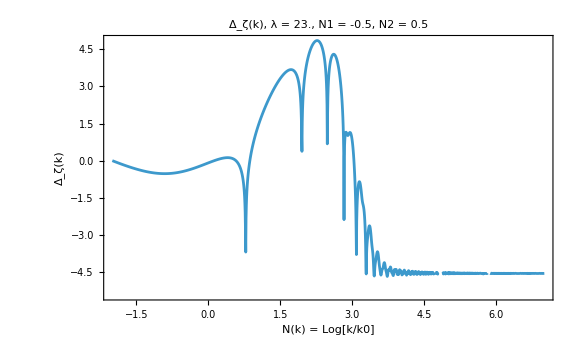

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.9919761248708639+2.4058402636321657 ⅈ,0.9919761248708639+«59» ⅈ,«59»+«59» ⅈ,-2.4172174530183025+0.9595683004525786 ⅈ},{«1»},{«1»},{«1»}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Divide::infy: Infinite expression -(1.×10^16+0``-15.856228414466853 ⅈ)/(0``-32.39680133271996) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Divide::infy: Infinite expression (1.×10^16+0``-15.856228414466853 ⅈ)/(0``-32.39680133271996) encountered.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Norm::mindet: Input matrix contains an indeterminate entry.

Divide::infy: Infinite expression -(0``-16.00317517101525+1.×10^16 ⅈ)/(0``-32.52221626540047) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Norm::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Norm::mindet will be suppressed during this calculation.

Norm::ptype: The second argument of Norm, 2., should be a symbol, Infinity or an integer or real number not less than 1 for vector p-norms; or 1, 2, Infinity or "Frobenius" for matrix norms.

General::stop: Further output of Norm::ptype will be suppressed during this calculation.

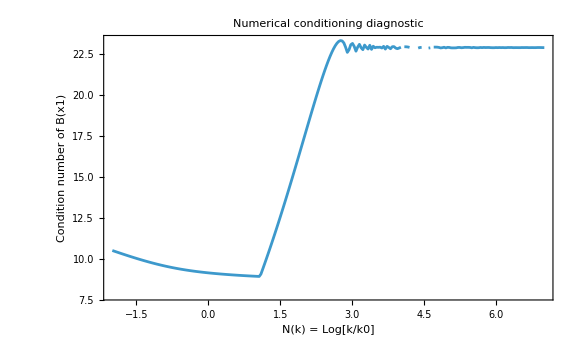

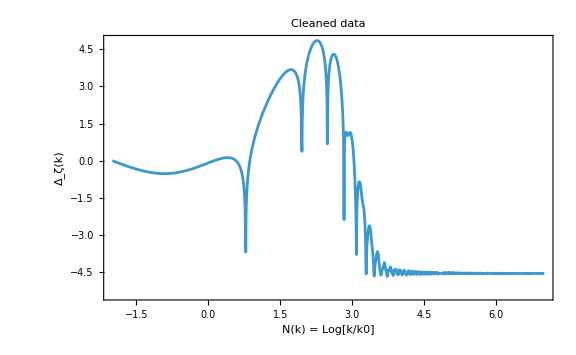

```mathematica
(* ============================================================*)(*PRL-style plot from analytic Bogoliubov basis*)(*Rectangular feature between N1 and N2*)(*Uses Nplot=Log[k/k0] as horizontal variable*)(* ============================================================*)Clear[xOfKN,k0OfN1N2,kOfNplot,x1OfNplot,x2OfNplot,lambdaSymbol,xSymbol,Vin1,Vin2,Vout1FromNplot,Vout2FromNplot,DeltaZetaFromNplot,NplotMin,NplotMax,nPts,NplotValues,rawDeltaZetaData,normPoint,deltaZetaData,lamVal,N1Val,N2Val,HVal,wp,conditionNumberAtNplot,conditionData,goodDeltaZetaData];

(*------------------------------------------------------------*)
(*Symbols used inside fullSystemBasis*)
(*Change these if your notebook uses different names*)
(*------------------------------------------------------------*)

lambdaSymbol=lam;
xSymbol=x;

(*Your basis matrix with row-vector convention:V^(i)(x)=c^(i).Bmat*)

(*Initial quantum modes*)
Vin1={1,0,0,0};
Vin2={0,0,1,0};

(*------------------------------------------------------------*)
(*Mapping between k,N,and x*)
(*------------------------------------------------------------*)

(*x(k,N)=(k/H) Exp[-N]*)
xOfKN[kval_?NumericQ,Hval_?NumericQ,Nval_?NumericQ]:=(kval/Hval) Exp[-Nval];

(*k0 is the mode that crosses the horizon at the middle of the feature*)
k0OfN1N2[Hval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ]:=Hval Exp[(N1val+N2val)/2];

(*Horizontal variable used in the PRL plot:Nplot=Log[k/k0]*)
kOfNplot[NplotVal_?NumericQ,Hval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ]:=k0OfN1N2[Hval,N1val,N2val] Exp[NplotVal];

(*Matching points in x,written in terms of Nplot*)
x1OfNplot[NplotVal_?NumericQ,N1val_?NumericQ,N2val_?NumericQ]:=Exp[NplotVal+(N2val-N1val)/2];

x2OfNplot[NplotVal_?NumericQ,N1val_?NumericQ,N2val_?NumericQ]:=Exp[NplotVal-(N2val-N1val)/2];

(*------------------------------------------------------------*)
(*Out-region vectors*)
(*------------------------------------------------------------*)

Vout1FromNplot[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,NplotVal_?NumericQ,wpval_:80]:=Module[{x1val,x2val,B1,B2,c1},x1val=SetPrecision[x1OfNplot[NplotVal,N1val,N2val],wpval];
x2val=SetPrecision[x2OfNplot[NplotVal,N1val,N2val],wpval];
B1=N[Bmat/. {lambdaSymbol->SetPrecision[lamval,wpval],xSymbol->x1val},wpval];
B2=N[Bmat/. {lambdaSymbol->SetPrecision[lamval,wpval],xSymbol->x2val},wpval];
(*Row convention:c.B1==Vin1 so Transpose[B1].c==Vin1*)c1=LinearSolve[Transpose[B1],SetPrecision[Vin1,wpval],Method->"Direct"];
Chop[c1.B2,10^(-Floor[wpval/3])]]

Vout2FromNplot[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,NplotVal_?NumericQ,wpval_:80]:=Module[{x1val,x2val,B1,B2,c2},x1val=SetPrecision[x1OfNplot[NplotVal,N1val,N2val],wpval];
x2val=SetPrecision[x2OfNplot[NplotVal,N1val,N2val],wpval];
B1=N[Bmat/. {lambdaSymbol->SetPrecision[lamval,wpval],xSymbol->x1val},wpval];
B2=N[Bmat/. {lambdaSymbol->SetPrecision[lamval,wpval],xSymbol->x2val},wpval];
c2=LinearSolve[Transpose[B1],SetPrecision[Vin2,wpval],Method->"Direct"];
Chop[c2.B2,10^(-Floor[wpval/3])]]

(*------------------------------------------------------------*)
(*Dimensionless curvature enhancement*)
(*Delta_zeta=P_zeta/P0*)
(*------------------------------------------------------------*)

DeltaZetaFromNplot[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,NplotVal_?NumericQ,wpval_:80]:=Module[{v1,v2,result},v1=Vout1FromNplot[lamval,N1val,N2val,NplotVal,wpval];
v2=Vout2FromNplot[lamval,N1val,N2val,NplotVal,wpval];
result=Abs[v1[[1]]+v1[[2]]]^2+Abs[v2[[1]]+v2[[2]]]^2;
Re[Chop[result,10^(-Floor[wpval/3])]]]

(*------------------------------------------------------------*)
(*Optional diagnostic:condition number of B(x1)*)
(*------------------------------------------------------------*)

conditionNumberAtNplot[lamval_?NumericQ,N1val_?NumericQ,N2val_?NumericQ,NplotVal_?NumericQ,wpval_:80]:=Module[{x1val,B1},x1val=SetPrecision[x1OfNplot[NplotVal,N1val,N2val],wpval];
B1=N[Bmat/. {lambdaSymbol->SetPrecision[lamval,wpval],xSymbol->x1val},wpval];
Norm[B1,2] Norm[Inverse[B1],2]]

(*------------------------------------------------------------*)
(*Numerical choices*)
(*------------------------------------------------------------*)

(*Example comparable in total angle to the lower PRL panel:PRL lower panel roughly uses lambda0=23,deltaN=1. Here keep N1,N2 independent,with N2-N1=1.*)
lamVal=23.0;
N1Val=-0.5;
N2Val=0.5;

HVal=1.0;
wp=100;

(*Horizontal range:PRL-style N(k)=Log[k/k0]*)
NplotMin=-2.0;
NplotMax=7.0;

(*Use many points,because the oscillations can be rapid*)
nPts=1500;

NplotValues=Subdivide[NplotMin,NplotMax,nPts-1];

(*------------------------------------------------------------*)
(*Evaluate data first*)
(*------------------------------------------------------------*)

rawDeltaZetaData=Table[{NplotVal,DeltaZetaFromNplot[lamVal,N1Val,N2Val,NplotVal,wp]},{NplotVal,NplotValues}];

(*Normalize by the leftmost value,mimicking normalization to the CMB/large-scale amplitude.*)
normPoint=rawDeltaZetaData[[1,2]];

deltaZetaData=rawDeltaZetaData/. {n_,y_}:>{n,y/normPoint};

(*Save data*)
Export["DeltaZeta_PRLStyle_vs_Nk.csv",deltaZetaData];

DumpSave["DeltaZeta_PRLStyleData.mx",{deltaZetaData,rawDeltaZetaData,normPoint,lamVal,N1Val,N2Val,HVal,wp}];

(*------------------------------------------------------------*)
(*Plot:PRL-style*)
(*------------------------------------------------------------*)

ListLinePlot[deltaZetaData,Frame->True,Joined->True,PlotRange->All,ScalingFunctions->{None,"Log10"},FrameLabel->{"N(k) = Log[k/k0]","\!\(\*SubscriptBox[\(Δ\), \(ζ\)]\)(k)"},PlotLabel->Row[{"\!\(\*SubscriptBox[\(Δ\), \(ζ\)]\)(k),  ","λ = ",lamVal,",  N1 = ",N1Val,",  N2 = ",N2Val}],ImageSize->Large]

(*------------------------------------------------------------*)
(*Optional:condition-number diagnostic*)
(*------------------------------------------------------------*)

conditionData=Table[{NplotVal,conditionNumberAtNplot[lamVal,N1Val,N2Val,NplotVal,60]},{NplotVal,Subdivide[NplotMin,NplotMax,250]}];

ListLinePlot[conditionData,Frame->True,Joined->True,PlotRange->All,ScalingFunctions->{None,"Log10"},FrameLabel->{"N(k) = Log[k/k0]","Condition number of B(x1)"},PlotLabel->"Numerical conditioning diagnostic",ImageSize->Large]

(*------------------------------------------------------------*)
(*Optional:remove points with non-positive or non-numeric data*)
(*before log plotting,if needed*)
(*------------------------------------------------------------*)

goodDeltaZetaData=Select[deltaZetaData,NumericQ[#[[2]]]&&#[[2]]>0&];

ListLinePlot[goodDeltaZetaData,Frame->True,Joined->True,PlotRange->All,ScalingFunctions->{None,"Log10"},FrameLabel->{"N(k) = Log[k/k0]","\!\(\*SubscriptBox[\(Δ\), \(ζ\)]\)(k)"},PlotLabel->"Cleaned data",ImageSize->Large]
```

```mathematica
(* ============================================================*)(*Strong brief-turn limit from already-computed Vout1,Vout2*)(*Goal:deltaN->0,lambda->Infinity,lambda deltaN fixed*)(* ============================================================*)Clear[deltaN,theta,lambdaEff,Nmid,Nk,k,k0,H,N1Rule,N2Rule,k0Rule,x1Rule,x2Rule,strongBriefRules,Czetain,Cpsiin,CzetainBriefRaw,CpsiinBriefRaw,CzetainBrief,CpsiinBrief,zetaFieldLateBrief,tryLimit,trySeries,maxTime];

(*------------------------------------------------------------*)
(*Symbols used in your notebook*)
(*Change these if your notebook uses different names*)
(*------------------------------------------------------------*)

lambdaSymbol=lam;
N1Symbol=N1;
N2Symbol=N2;

(*If your expressions contain x1 and x2 explicitly,keep these.If not,these rules simply do nothing.*)
x1Symbol=x1;
x2Symbol=x2;

(*------------------------------------------------------------*)
(*Late-time zeta coefficients*)
(*------------------------------------------------------------*)

(*Convention:Vout1={zeta1Out^(1),zeta2Out^(1),psi1Out^(1),psi2Out^(1)} Vout2={zeta1Out^(2),zeta2Out^(2),psi1Out^(2),psi2Out^(2)}*)

Czetain=Vout1[[1]]+Vout1[[2]];
Cpsiin=Vout2[[1]]+Vout2[[2]];

(*These are the coefficients multiplying a_zeta(k) and a_psi(k) in the late-time zeta field:zeta_c(k)=i H/Sqrt[2 k^3] (Czetain a_zeta(k)+Cpsiin a_psi(k))+h.c.(-k)*)

(*------------------------------------------------------------*)
(*PRL variables*)
(*------------------------------------------------------------*)

(*The feature is centered at Nmid and has width deltaN*)
N1Rule=N1Symbol->Nmid-deltaN/2;
N2Rule=N2Symbol->Nmid+deltaN/2;

(*k0 is the mode crossing the horizon at the middle of the turn*)
k0Rule=k0->H Exp[Nmid];

(*PRL horizontal variable:Nk=Log[k/k0],so k=k0 Exp[Nk].*)
kRule=k->k0 Exp[Nk];

(*Matching points in x.x=(k/H) Exp[-N].After k=k0 Exp[Nk] and k0=H Exp[Nmid],we get x1=Exp[Nk+deltaN/2],x2=Exp[Nk-deltaN/2].*)
x1Rule=x1Symbol->Exp[Nk+deltaN/2];
x2Rule=x2Symbol->Exp[Nk-deltaN/2];

(*Strong brief-turn scaling.Keep theta=lambda deltaN fixed.In PRL notation,theta=lambda0 deltaN=2 delta theta.*)
lambdaEff=theta/deltaN;

strongBriefRules={N1Rule,N2Rule,k0Rule,kRule,x1Rule,x2Rule,lambdaSymbol->lambdaEff};

(*------------------------------------------------------------*)
(*Apply replacements*)
(*------------------------------------------------------------*)

CzetainBriefRaw=Czetain/. strongBriefRules;
CpsiinBriefRaw=Cpsiin/. strongBriefRules;

(*------------------------------------------------------------*)
(*Try the strong brief-turn limit*)
(*------------------------------------------------------------*)

maxTime=300;

tryLimit[expr_]:=TimeConstrained[Assuming[{theta>0,H>0,k0>0,Element[Nk,Reals],deltaN>0},Limit[expr,deltaN->0,Direction->"FromAbove"]],maxTime,$Failed];

trySeries[expr_]:=TimeConstrained[Assuming[{theta>0,H>0,k0>0,Element[Nk,Reals],deltaN>0},Normal[Series[expr,{deltaN,0,0}]]],maxTime,$Failed];

CzetainBrief=tryLimit[CzetainBriefRaw];

If[CzetainBrief===$Failed,CzetainBrief=trySeries[CzetainBriefRaw];];

CpsiinBrief=tryLimit[CpsiinBriefRaw];

If[CpsiinBrief===$Failed,CpsiinBrief=trySeries[CpsiinBriefRaw];];

(*Display the candidate brief-turn coefficients*)
CzetainBrief//TraditionalForm
CpsiinBrief//TraditionalForm

(*------------------------------------------------------------*)
(*Late-time zeta field in the strong brief-turn limit*)
(*------------------------------------------------------------*)

zetaFieldLateBrief=I H/Sqrt[2 k^3] (CzetainBrief aZeta[k]+CpsiinBrief aPsi[k])+HC[-k];

zetaFieldLateBrief//TraditionalForm

(* ============================================================*)
(*If the symbolic limit fails,do a numerical scaling test*)
(* ============================================================*)

Clear[CzetainBriefNumeric,CpsiinBriefNumeric,deltaNValues,thetaVal,NkVal,HVal,CzetainScalingData,CpsiinScalingData];

(*Numerical version of the strong scaling:lambda=theta/deltaN,N1=Nmid-deltaN/2,N2=Nmid+deltaN/2.*)

CzetainBriefNumeric[thetaVal_?NumericQ,deltaNVal_?NumericQ,NkVal_?NumericQ,HVal_?NumericQ,NmidVal_:0]:=N[Czetain/. {lambdaSymbol->thetaVal/deltaNVal,N1Symbol->NmidVal-deltaNVal/2,N2Symbol->NmidVal+deltaNVal/2,k0->HVal Exp[NmidVal],k->HVal Exp[NmidVal] Exp[NkVal],x1Symbol->Exp[NkVal+deltaNVal/2],x2Symbol->Exp[NkVal-deltaNVal/2],H->HVal},80];

CpsiinBriefNumeric[thetaVal_?NumericQ,deltaNVal_?NumericQ,NkVal_?NumericQ,HVal_?NumericQ,NmidVal_:0]:=N[Cpsiin/. {lambdaSymbol->thetaVal/deltaNVal,N1Symbol->NmidVal-deltaNVal/2,N2Symbol->NmidVal+deltaNVal/2,k0->HVal Exp[NmidVal],k->HVal Exp[NmidVal] Exp[NkVal],x1Symbol->Exp[NkVal+deltaNVal/2],x2Symbol->Exp[NkVal-deltaNVal/2],H->HVal},80];

(*Choose a fixed total turn strength theta=lambda deltaN*)
thetaVal=23.0;
NkVal=2.0;
HVal=1.0;

deltaNValues={0.5,0.25,0.1,0.05,0.025,0.01};

CzetainScalingData=Table[{dN,CzetainBriefNumeric[thetaVal,dN,NkVal,HVal]},{dN,deltaNValues}];

CpsiinScalingData=Table[{dN,CpsiinBriefNumeric[thetaVal,dN,NkVal,HVal]},{dN,deltaNValues}];

CzetainScalingData//TableForm
CpsiinScalingData//TableForm

(*The values should approach a stable limit as deltaN->0 if the hypergeometric expressions can numerically resolve the strong brief-turn scaling.*)

(* ============================================================*)
(*Optional:normalized power enhancement in the same scaling*)
(* ============================================================*)

Clear[DeltaZetaStrongBriefNumeric];

DeltaZetaStrongBriefNumeric[thetaVal_?NumericQ,deltaNVal_?NumericQ,NkVal_?NumericQ,HVal_?NumericQ,NmidVal_:0]:=Module[{cz,cp},cz=CzetainBriefNumeric[thetaVal,deltaNVal,NkVal,HVal,NmidVal];
cp=CpsiinBriefNumeric[thetaVal,deltaNVal,NkVal,HVal,NmidVal];
Re[Chop[Abs[cz]^2+Abs[cp]^2]]];

Table[{dN,DeltaZetaStrongBriefNumeric[thetaVal,dN,NkVal,HVal]},{dN,deltaNValues}]//TableForm
```